# Assignment 4 No.5 (a)

```mathematica
x=(Cos[t])^2
```

Cos[t]^2

```mathematica
y=Cos[t]
```

Cos[t]

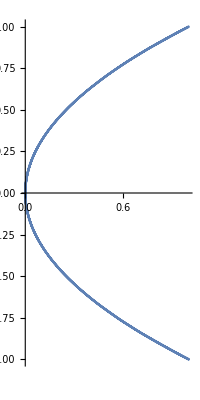

```mathematica
ParametricPlot[{x,y},{t,0,4π}]
```

```mathematica
(b)
L=∫_a^b √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt
```

```mathematica
D[Cos[t]^2,t]
```

-2 Cos[t] Sin[t]

```mathematica
D[Cos[t],t]
```

-Sin[t]

```mathematica
L=∫_0^(4π) √((-2 Cos[t] Sin[t])^2+(-Sin[t])^2)ⅆt//N
```

11.8315

i.e, 11.8315 meters

## (c) about x axis. S=∫_a^b 2Pi yⅆs where ds=√((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=a (Cos[θ])^3
```

a Cos[θ]^3

```mathematica
y=a (Sin[θ])^3
```

a Sin[θ]^3

```mathematica
D[a Cos[θ]^3,θ]
```

-3 a Cos[θ]^2 Sin[θ]

```mathematica
D[a Sin[θ]^3,θ]
```

3 a Cos[θ] Sin[θ]^2

```mathematica
S=∫_0^(π/2) 2Pi a Sin[θ]^3 √((-3 a Cos[θ]^2 Sin[θ])^2+(3 a Cos[θ] Sin[θ]^2)^2)ⅆθ
```

6/5 a √(a^2) π

6/5 a √(a^2) π meter^2  (Ans.)